```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;rep={kx-> k Sin[θ] Cos[ϕ],ky-> k Sin[θ]Sin[ϕ],kp-> k Sin[θ],kz-> k Cos[θ]};
ass=Assumptions->{ϵ,kx,ky,kz,α,θ,d}∈ Reals  && ϵ>0 ;
repl={a1->Subscript[a, 1],a2->Subscript[a, 2],a3->Subscript[a, 3],a4->Subscript[a, 4],kx->Subscript[k, x],ky->Subscript[k, y],kz->Subscript[k, z], d->Δ};
```

## Topological Hopf: Odd number of BC-dipoles in BZ

```mathematica
Clear[ham];(* {ckx,cky,ckz}={Cos[kx],Cos[ky],Cos[kz]};{skx,sky,skz}={Sin[kx],Sin[ky],Sin[kz]}; *)
ham=(*({{0, Sin[kx]-ⅈ Sin[ky], d-ⅈ Sin[kz]}, {Sin[kx]+ⅈ Sin[ky], 0, 0}, {d+ⅈ Sin[kz], 0, 0}})*)(*({{0, Sin[kx]-ⅈ Sin[ky], d+Cos[kx]+Cos[ky]+Cos[kz]-ⅈ Sin[kz]}, {Sin[kx]+ⅈ Sin[ky], 0, 0}, {d+Cos[kx]+Cos[ky]+Cos[kz]+ⅈ Sin[kz], 0, 0}})*)
({{0, skx-ⅈ sky, d+ckx+cky+ckz-ⅈ skz}, {skx+ⅈ sky, 0, 0}, {d+ckx+cky+ckz+ⅈ skz, 0, 0}});
{es,evec}=FullSimplify[Eigensystem[ham],ass] ;
FullSimplify[es/.d->d,ass](* -Graphics- *)
Clear[d];
```

{0,-√((ckx+cky+ckz+d)^2+skx^2+sky^2+skz^2),√((ckx+cky+ckz+d)^2+skx^2+sky^2+skz^2)}

```mathematica
hnh=({{0, skx-ⅈ sky, d+ckx+cky+ckz-ⅈ skz+ⅈ a}, {skx+ⅈ sky, 0, 0}, {d+ckx+cky+ckz+ⅈ skz+ⅈ a, 0, 0}});
FullSimplify[Eigenvalues[hnh]]
```

{0,-√(-(a-ⅈ (ckx+cky+ckz+d))^2+skx^2+sky^2+skz^2),√(-(a-ⅈ (ckx+cky+ckz+d))^2+skx^2+sky^2+skz^2)}

```mathematica
Clear[d,esq,eq,sol,a];
esq[a_,d_]=FullSimplify[-(a-ⅈ (ckx+cky+ckz+d))^2+skx^2+sky^2+skz^2];
eq[a_,d_]=(FullSimplify[ComplexExpand[ReIm[esq[a,d]/.{skx^2->1-ckx^2,sky^2->1-cky^2,skz^2->1-ckz^2}]]])/.{ckx->Cos[kx],cky->Cos[ky],ckz->Cos[kz]}
```

{3-a^2+d^2+2 Cos[ky] Cos[kz]+2 d (Cos[ky]+Cos[kz])+2 Cos[kx] (d+Cos[ky]+Cos[kz]),2 a (d+Cos[kx]+Cos[ky]+Cos[kz])}

```mathematica
expr=eq[a,d][[2]]/.repl
TeXForm[expr]
```

2 a (Δ+Cos[k_x]+Cos[k_y]+Cos[k_z])

```mathematica
(* limit on a for d=-1*)
FullSimplify[Reduce[5-2 a^2+(2-3 ckz) ckz>=0 && -1<=ckz<=1,a]]
(*%/.ckz->Cos[kz]*)
```

(ckz==-1&&a==0)||(-1<ckz≤1&&-√(5/2+ckz-(3 ckz^2)/2)≤a≤√(5/2+ckz-(3 ckz^2)/2))

```mathematica
ArcCos[sol[Cos[0],1.15]]
```

{{2.19201,0.949583},{0.949583,2.19201}}

```mathematica
a=1;d=1(* -Graphics- *);(*lim1=0;lim2=2π;*)lim1=-π;lim2=π;
eqn=eq[a,d];
	c1= ContourPlot3D[eqn[[1]]==0,{kx,lim1,lim2},{ky,lim1,lim2},{kz,lim1,lim2},Mesh->None,ContourStyle->Directive[Darker[Blue],Opacity[0.8],Specularity[White,30]]];

c2= ContourPlot3D[eqn[[2]]==0,{kx,lim1,lim2},{ky,lim1,lim2},{kz,lim1,lim2},Mesh->None,ContourStyle->Directive[Orange,Opacity[0.5],Specularity[White,30]]];
pd1=Show[{c2,c1},TicksStyle->Directive[Gray,Bold,18,FontFamily->"Times"],AxesLabel->(Style[#,Black,Bold,22,FontFamily->"Times"]&/@{"k_x","k_y","k_z"}),ImageSize->400,ViewPoint->{1.4330301079592185,-2.5301907176784355,1.7304795987980544}]
Clear[a,d,ckx,cky,ckz];
```

```mathematica
AbsoluteOptions[]
```

```mathematica
a=0.75;d=-1(* -Graphics- *);lim=π;
eqn=eq[a,d];
	c1= ContourPlot3D[eqn[[1]]==0,{kx,-lim,lim},{ky,-lim,lim},{kz,-lim,lim},PlotLegends->Automatic,Mesh->None,ContourStyle->Directive[Darker[Blue],Opacity[0.8],Specularity[White,30]]];

c2= ContourPlot3D[eqn[[2]]==0,{kx,-lim,lim},{ky,-lim,lim},{kz,-lim,lim},PlotLegends->Automatic,Mesh->None,ContourStyle->Directive[Orange,Opacity[0.5],Specularity[White,30]]];
pd2=Show[{c2,c1},TicksStyle->Directive[Gray,Bold,18,FontFamily->"Times"],AxesLabel->(Style[#,Black,Bold,22,FontFamily->"Times"]&/@{"k_x","k_y","k_z"}),ImageSize->400,ViewPoint->{1.4330301079592185,-2.530190717678435,1.7304795987980544}]
Clear[a,d];
```

```mathematica
SetDirectory[NotebookDirectory[]];
plt=-Graphics3D-;
Export["epdipole.pdf",Rasterize[plt,Background->None],ImageResolution->100];
```

```mathematica
eqn=eq[2.5,0.5]/.kz->0.7;
lim=π;
c1=ContourPlot[{eqn[[1]]==0},{kx,-lim,lim},{ky,-lim,lim},ContourStyle->Blue];
c2=ContourPlot[{eqn[[2]]==0},{kx,-lim,lim},{ky,-lim,lim},ContourStyle->Green];

d1=DensityPlot[Abs[eqn[[1]]],{kx,-lim,lim},{ky,-lim,lim},ColorFunction->ColorData[{"SunsetColors",{3,0}}],ColorFunctionScaling->False,PlotLegends->Automatic];
d2=DensityPlot[Abs[eqn[[2]]],{kx,-lim,lim},{ky,-lim,lim},ColorFunction->ColorData[{"SunsetColors",{3,0}}],ColorFunctionScaling->False,PlotLegends->Automatic];
Show[d1,c1]
Show[d2,c2]
Show[c1,c2]
```

```mathematica
eqn=eq[0.75,-1]/.kz->0;
lim=π;
c1=ContourPlot[{eqn[[1]]==0},{kx,-lim,lim},{ky,-lim,lim},ContourStyle->LightBlue];
c2=ContourPlot[{eqn[[2]]==0},{kx,-lim,lim},{ky,-lim,lim},ContourStyle->LightGreen];

d1=DensityPlot[Abs[eqn[[1]]],{kx,-lim,lim},{ky,-lim,lim},ColorFunction->ColorData[{"SunsetColors",{3,0}}],ColorFunctionScaling->False,PlotLegends->Automatic];
d2=DensityPlot[Abs[eqn[[2]]],{kx,-lim,lim},{ky,-lim,lim},ColorFunction->ColorData[{"SunsetColors",{3,0}}],ColorFunctionScaling->False,PlotLegends->Automatic];
Show[d1,c1]
Show[d2,c2]
Show[c1,c2]
```

## Valley latt model

```mathematica
(*({{0, Sin[kx]+ⅈ Sin[ky], -ⅈ Sin[kz]-ⅈ a}, {Sin[kx]-ⅈ Sin[ky], 0, 0}, {ⅈ Sin[kz]-ⅈ a, 0, 0}})*)
```

```mathematica
Clear[ham];
hamil=({{0, skx+ⅈ sky, -ⅈ skz-ⅈ a}, {skx-ⅈ sky, 0, 0}, {ⅈ skz-ⅈ a, 0, 0}});
{es,evec}=FullSimplify[Eigensystem[hamil],ass] ;
FullSimplify[es,ass]/.{skx->Sin[kx],sky->Sin[ky],skz->Sin[kz]}
Clear[d];
```

{0,-√(-a^2+Sin[kx]^2+Sin[ky]^2+Sin[kz]^2),√(-a^2+Sin[kx]^2+Sin[ky]^2+Sin[kz]^2)}

```mathematica
expr=FullSimplify[-a^2+Sin[kx]^2+Sin[ky]^2+Sin[kz]^2/.repl]
TeXForm[expr]
```

-a^2+Sin[k_x]^2+Sin[k_y]^2+Sin[k_z]^2

-a^2+\sin ^2\left(k_x\right)+\sin ^2\left(k_y\right)+\sin ^2\left(k_z\right)

```mathematica
(* https://www.researchgate.net/publication/351969770_Symmetry-enforced_band_crossings_in_tetragonal_materials_Dirac_and_Weyl_degeneracies_on_points_lines_and_planes/figures?lo=1
-Graphics-
Brillouin zones of the tetragonal crystal system.TRIMs are labeled in dark blue.Lines of high symmetry,i.e.,sections of rotation axes,are highlighted for the fourfold rotation (red) along[001],and the twofold rotations along 100 (green),110 (light blue),and[001] (orange).(a) Primitive BZ.(b) Body-centered BZ for c<a,BCT 1.(c) Body-centered BZ for c>a,BCT 2.
*)
```

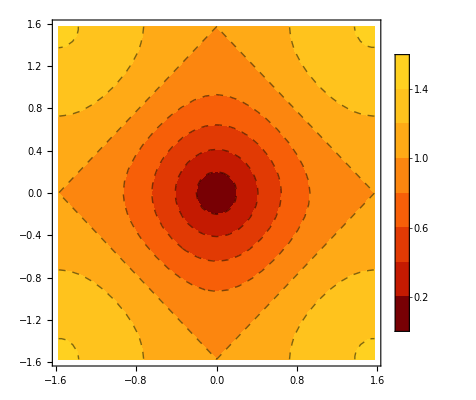

```mathematica
aval=0.;e1={(√3)/2,1/2};e2={(√3)/2,-1/2};

lim=π/2;p0=ContourPlot[Re[√(Sin[qx]^2+Sin[qy]^2-aval^2)],{qx,-lim,lim},{qy,-lim,lim},LabelStyle->Directive[FontSize->16,FontFamily->"Times",Bold, Gray],AspectRatio->Automatic,MaxRecursion->1,Frame->True,ContourStyle->Dashed,PlotLegends->Automatic,ColorFunction->"SolarColors"(*ColorFunction->ColorData[{"SunsetColors",{1,0}}],ColorFunctionScaling->False*)]
```

```mathematica
p01=ContourPlot[Sin[qx]^2+Sin[qy]^2==aval^2,{qx,-(4π)/3,(4π)/3},{qy,-(2π)/(√3),(2π)/(√3)},RegionFunction->Function[{qx,qy,z},-(2π)/(√3)<{qx,qy}.e1<(2π)/(√3)&&-(2π)/(√3)<{qx,qy}.e2<(2π)/(√3)], AspectRatio->Automatic,ContourStyle->Directive[White,Dashing[0.006],Thickness[0.007]],PlotLegends->Automatic];
p1=Show[p0,p01]
```

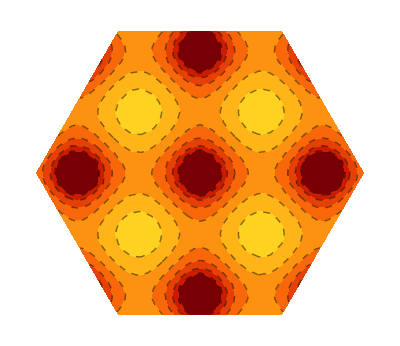

```mathematica
aval=.5;e1={(√3)/2,1/2};e2={(√3)/2,-1/2};p0=ContourPlot[Re[√(Sin[qx]^2+Sin[qy]^2-aval^2)],{qx,-(4π)/3,(4π)/3},{qy,-(2π)/(√3),(2π)/(√3)},RegionFunction->Function[{qx,qy,z},-(2π)/(√3)<{qx,qy}.e1<(2π)/(√3)&&-(2π)/(√3)<{qx,qy}.e2<(2π)/(√3)],(*LabelStyle->Directive[FontSize->18,FontFamily->"Times",Bold, Gray],*)AspectRatio->Automatic,MaxRecursion->1,Frame->None,ContourStyle->Dashed,ColorFunction->"SolarColors",PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[FontSize->18,FontFamily->"Times",Bold, Gray],LegendLayout->"Row",LegendMarkerSize->300],Below]]
```

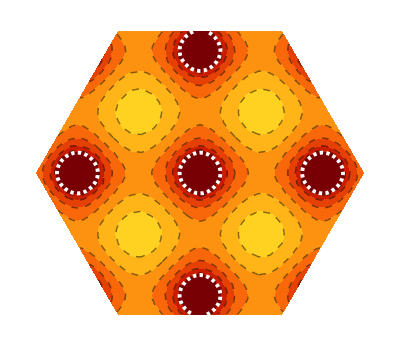

```mathematica
p01=ContourPlot[Sin[qx]^2+Sin[qy]^2==aval^2,{qx,-(4π)/3,(4π)/3},{qy,-(2π)/(√3),(2π)/(√3)},RegionFunction->Function[{qx,qy,z},-(2π)/(√3)<{qx,qy}.e1<(2π)/(√3)&&-(2π)/(√3)<{qx,qy}.e2<(2π)/(√3)], AspectRatio->Automatic,ContourStyle->Directive[White,Dashing[0.006],Thickness[0.007]]];
p1=Show[p0,p01]
SetDirectory[NotebookDirectory[]];
Export["epdipole2.pdf",Rasterize[p1,Background->None],ImageResolution->100];
```